# One Piece Cody

```mathematica
centers[p1_,p2_,R_]:={x,y}/.Solve[{(p1⟦1⟧-x)^2+(p1⟦2⟧-y)^2==R^2,(p2⟦1⟧-x)^2+(p2⟦2⟧-y)^2==R^2},{x,y}]
angles[p1_,p2_,center_]:={ArcTan[(p1-center)⟦1⟧,(p1-center)⟦2⟧],ArcTan[(p2-center)⟦1⟧,(p2-center)⟦2⟧]}
angles2[p1_,p2_,center_]:={angles[p1,p2,center]⟦2⟧,angles[p1,p2,center]⟦1⟧-2π}
circle[p1_,p2_,R_,index_]:=Circle[centers[p1,p2,R]⟦index⟧,R,angles[p1,p2,centers[p1,p2,R]⟦index⟧]]
circle2[p1_,p2_,R_,index_]:=Circle[centers[p1,p2,R]⟦index⟧,R,angles2[p1,p2,centers[p1,p2,R]⟦index⟧]]
line[p1_,p2_]:=Line[{p1,p2}]
```

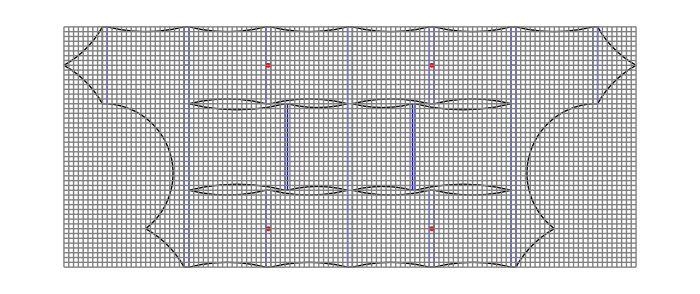

```mathematica
segments={
(*Left*)
circle[{250,0},{170,80},205,1],
circle[{170,80},{90,340},145,1],
line[{90,340},{80,340}],
circle[{80,340},{0,420},205,1],
circle[{0,420},{80,500},205,2],

(*Top*)
line[{80,500},{90,500}],
circle[{90,500},{250,500},325,2],
line[{250,500},{260,500}],
circle[{260,500},{420,500},325,2],
line[{420,500},{430,500}],
circle[{430,500},{590,500},325,2],
line[{590,500},{600,500}],
circle[{600,500},{760,500},325,2],
line[{760,500},{770,500}],
circle[{770,500},{930,500},325,2],
line[{930,500},{940,500}],
circle[{940,500},{1100,500},325,2],
line[{1100,500},{1110,500}],
circle[{1110,500},{1190,420},205,2],

(*Bottom*)
line[{250,0},{260,0}],
circle[{260,0},{420,0},325,1],
line[{420,0},{430,0}],
circle[{430,0},{590,0},325,1],
line[{590,0},{600,0}],
circle[{600,0},{760,0},325,1],
line[{760,0},{770,0}],
circle[{770,0},{930,0},325,1],
line[{930,0},{940,0}],

(*Right*)
circle[{940,0},{1020,80},205,2],
circle2[{1100,340},{1020,80},145,2],
line[{1100,340},{1110,340}],
circle[{1110,340},{1190,420},205,2],

(*Vertical internal*)
{Thin,Blue,
line[{80,340},{80,500}],
line[{90,340},{90,500}],
line[{250,0},{250,500}],
line[{260,0},{260,500}],
line[{420,340},{420,500}],
line[{430,340},{430,500}],
line[{420,0},{420,160}],
line[{430,0},{430,160}],
line[{460,160},{460,340}],
line[{465,160},{465,340}],
line[{590,0},{590,500}],
line[{600,0},{600,500}],
line[{725,160},{725,340}],
line[{730,160},{730,340}],
line[{760,0},{760,160}],
line[{770,0},{770,160}],
line[{760,340},{760,500}],
line[{770,340},{770,500}],
line[{930,0},{930,500}],
line[{940,0},{940,500}],
line[{1100,340},{1100,500}],
line[{1110,340},{1110,500}]},

(*Horizontal internal*)
circle[{260,160},{420,160},325,2],
line[{420,160},{430,160}],
circle[{430,160},{590,160},325,2],
circle[{600,160},{760,160},325,2],
line[{760,160},{770,160}],
circle[{770,160},{930,160},325,2],

circle[{260,340},{420,340},325,1],
line[{420,340},{430,340}],
circle[{430,340},{590,340},325,1],
circle[{600,340},{760,340},325,1],
line[{760,340},{770,340}],
circle[{770,340},{930,340},325,1],

circle[{260,160},{460,160},405,1],
line[{460,160},{465,160}],
circle[{465,160},{590,160},250,1],
circle[{600,160},{725,160},250,1],
line[{725,160},{730,160}],
circle[{730,160},{930,160},405,1],

circle[{260,340},{460,340},405,2],
line[{460,340},{465,340}],
circle[{465,340},{590,340},250,2],
circle[{600,340},{725,340},250,2],
line[{725,340},{730,340}],
circle[{730,340},{930,340},405,2],

(*Markings*)
line[{250,80},{260,80}],
line[{250,420},{260,420}],
line[{940,80},{930,80}],
line[{940,420},{930,420}],
{PointSize[1/200],Red,
Point[{425,80}],
Point[{425,420}],
Point[{765,80}],
Point[{765,420}]}
};

Graphics[{
{EdgeForm[Directive[Red,Thin]],Opacity[0],Rectangle[{0,0},{1190,500}]},
segments,
{Thin, Gray,Line[Table[{{x,0},{x,500}},{x,0,1190,10}]],Line[Table[{{0,y},{1190,y}},{y,0,500,10}]]}},ImageSize->700]
```